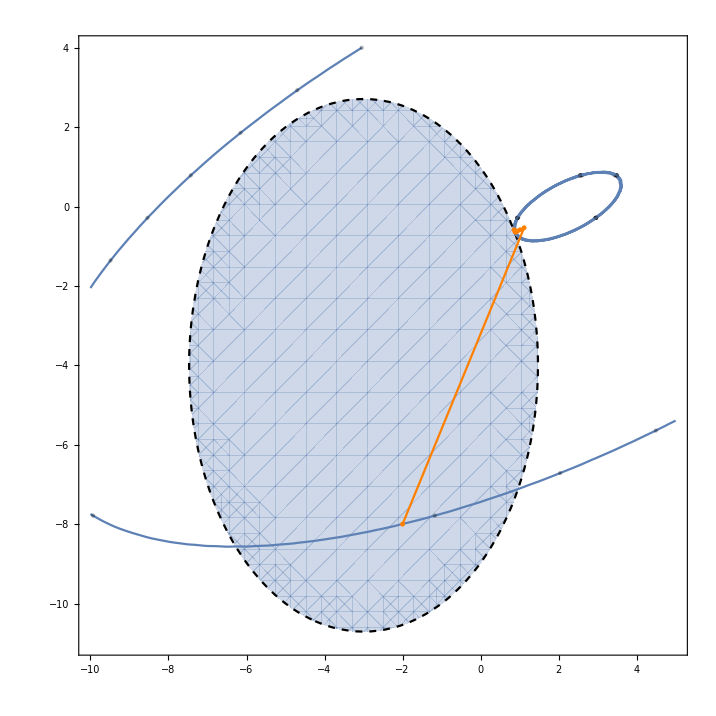

```mathematica
KvadpointsList =List[{},{}];
KvadlevelsList=List[];
RozpointsList =List[{},{}];
RozlevelsList=List[];
KvadpointsList=Import["C:/Users/Артем/Desktop/points_for_kvad.txt","Table"];
KvadlevelsList=Import["C:/Users/Артем/Desktop/level_lines_for_kvad.txt","Table"];
RozpointsList=Import["C:/Users/Артем/Desktop/points_for_roz.txt","Table"];
RozlevelsList=Import["C:/Users/Артем/Desktop/level_lines_for_roz.txt","Table"];
Kvadlistplot=List[];
Rozlistplot=List[];
rgp1 =RegionPlot[x>=0&&y>=2&&x+y<=10,{x,-2,12},{y,-2,12}, BoundaryStyle->{Dashed, Black}];
rgp2 =RegionPlot[((x+3)^2)/4+((y+4)^2)/9<5,{x,-10,5},{y,-11,4}, BoundaryStyle->{Dashed, Black}];
For[i=1,i<=Length[KvadlevelsList],++i,AppendTo[Kvadlistplot,ContourPlot[2x^2-4x*y+5y^2-4*Sqrt[5](x-y)+4==Part[Part[KvadlevelsList,i],1],{x,-10,5},{y,-11,4},Mesh->Full,GridLines->Automatic]]];
Show[rgp2,Kvadlistplot, ListLinePlot[KvadpointsList,PlotStyle->Orange,PlotRange->Full, PlotMarkers->{Automatic,5},GridLines->Automatic]]
```

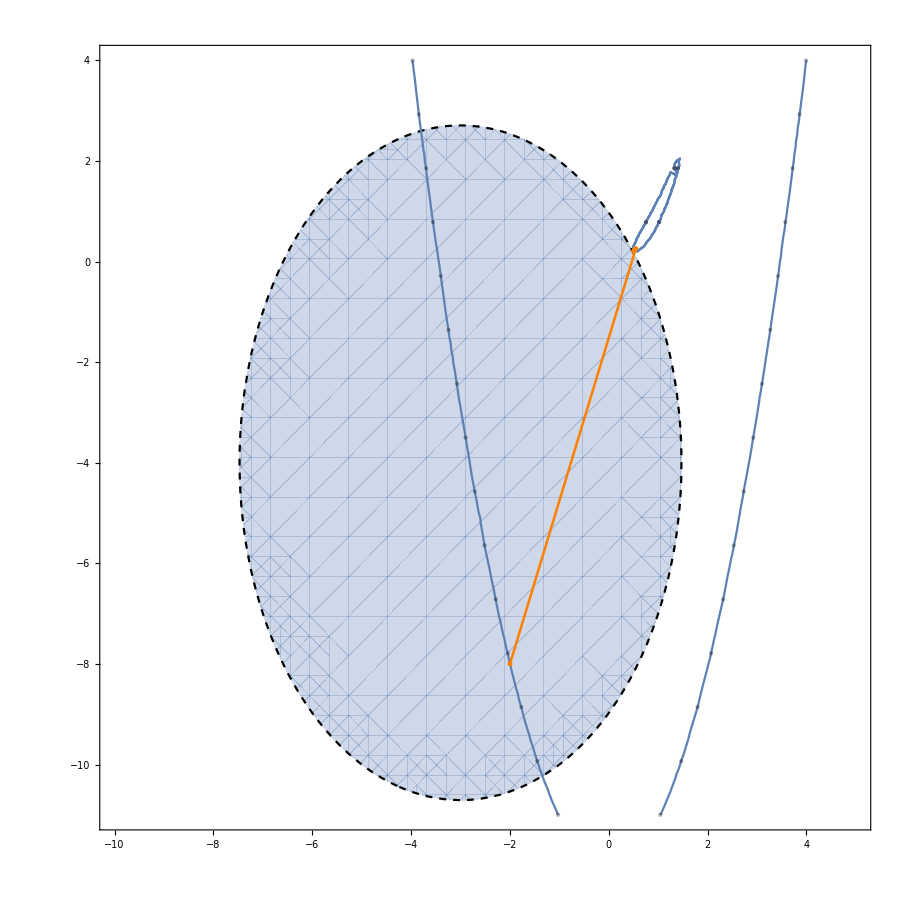

```mathematica
For[i=1,i<=Length[RozlevelsList],++i,AppendTo[Rozlistplot,ContourPlot[4(x^2-y)^2+(x-1)^2==Part[Part[RozlevelsList,i],1],{x,-10,5},{y,-11,4},Mesh->Full,GridLines->Automatic]]];
Show[rgp2,Rozlistplot,ListLinePlot[RozpointsList,PlotStyle->{Orange, Thickness[0.002]},PlotRange->Full, PlotMarkers->{Automatic,5},GridLines->Automatic]]
```

```mathematica
Expand[D[D[a(x^2-y)^2+(x-1)^2,y],y]]
```

2 a

```mathematica
l1={{Expand[D[D[a(x^2-y)^2+(x-1)^2,x],x]],Expand[D[D[a(x^2-y)^2+(x-1)^2,x],y]]},{
Expand[D[D[a(x^2-y)^2+(x-1)^2,y],x]],Expand[D[D[a(x^2-y)^2+(x-1)^2,y],y]]}}
```

{{2+12 a x^2-4 a y,-4 a x},{-4 a x,2 a}}

Set::wrsym: Symbol List is Protected.

{{2+12 a x^2-4 a y,-4 a x},{-4 a x,2 a}}

```mathematica
FullSimplify[Inverse[l1]]/.{x->0, y->0}
```

{{1/2,0},{0,1/(2 a)}}

```mathematica
{2+12 a x^2-4 a y,-4 a x,-4 a x,2 a}
```

{2+12 a x^2-4 a y,-4 a x,-4 a x,2 a}

```mathematica
D[]
```

D::argm: D called with 0 arguments; 1 or more arguments are expected.

D[]

```mathematica
Det[l1]
```

4 a+8 a^2 x^2-8 a^2 y

```mathematica
FindInstance[Det[l1]<0, {x,y,a}, Reals]
```

{{x→0,y→3/2,a→1}}

```mathematica
33
```

33

```mathematica
Orthogonalize[{{0.99999631597842498 ,-0.99999631597842498},{0.0000000000000000,-0.99999631597842498}}]//FullSimplify
```

{{0.707107,-0.707107},{-0.707107,-0.707107}}

```mathematica
Dot[0.999996315978425/(√({0.,-0.999996315978425}[0.999996315978425,0.999996315978425])),]
```

0.999996/(√({0.,-0.999996}[0.999996,0.999996])).Null

```mathematica
Show[ContourPlot[2x^2-4x*y+5y^2-4*Sqrt[5](x-y)+4==0,{x,-5,5},{y,-5,5},Filling->Top]]
```

ContourPlot::optx: Unknown option Filling→Top in ContourPlot[2 x^2-4 x y+5 y^2-4 √5 (x-y)+4==0,{x,-5,5},{y,-5,5},Filling→Top].

Show::gtype: ContourPlot is not a type of graphics.

Show[ContourPlot[2 x^2-4 x y+5 y^2-4 √5 (x-y)+4==0,{x,-5,5},{y,-5,5},Filling→Top]]

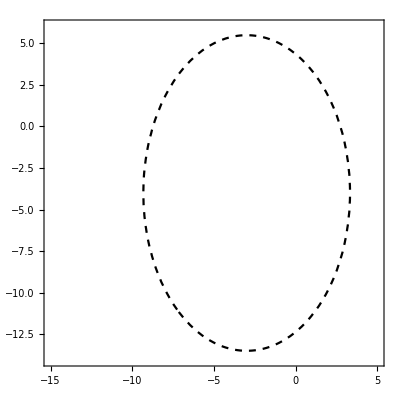

```mathematica
Show[ContourPlot[((x+3)^2)/4+((y+4)^2)/9==10,{x,-15,5},{y,-14,6}, ContourStyle->{Black, Dashed}]]
```